Equation (10)

```mathematica
ϕ0Func[M_,θB_,τR_,τT_]:=1-Exp[-4 M/θB(τR-τT)]
ϕ0FuncAlt1[M_,θB_,τR_,τT_]:=1-Exp[-2 M/θB(τR-τT)]
ϕ0FuncAlt2[M_,θB_,τR_,τT_]:=1-Exp[-M/θB(τR-τT)]
```

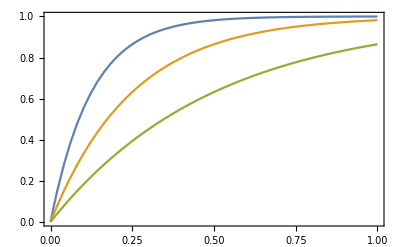

```mathematica
myθB:=0.01
myτR:=0.02
myτT:=0.
Plot[{
ϕ0Func[M,myθB,myτR,myτT],
ϕ0FuncAlt1[M,myθB,myτR,myτT],
ϕ0FuncAlt2[M,myθB,myτR,myτT]
},{M,0,1},
PlotRange->{Full,{0,1}},
Frame->True
]
```